TemporalData::rsmplng: The data is not uniformly spaced and will be automatically resampled to the resolution of the minimum time increment.

TimeSeriesModel[…]

TemporalData[…]

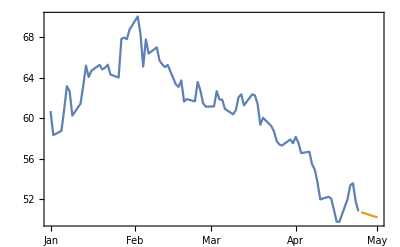

```mathematica
quotes=FinancialData["RUB=X","2015-01-01"];
series=TimeSeries[quotes];
model=TimeSeriesModelFit[series]
forecast=TimeSeriesForecast[model,{7}]
DateListPlot[{series,forecast},Joined->True]
```

```mathematica
InteractiveTradingChart[FinancialData["RUB=X","OHLCV","2015-01-01"],FinancialIndicator["MovingAverageEnvelopes"]]
```